# CRNSSA Demo

```mathematica
<<CRNSSA`;
?CRNSSA`*
```

## Reaction System 0: f(x) = 1

```mathematica
rxnsys0 = {
rxnl[{x},{y},1],
rxnl[{y,y},{y},1],
conc[{x, y},5]
};
SpeciesInRxnsys[rxnsys0]
```

{x,y}

{{{5,5},{5,4},{5,3},{4,4},{4,3},{3,4},{3,3},{3,2},{2,3},{2,2},{2,1},{1,2},{1,1},{0,2},{0,1}},{0.,0.0147828,0.0173464,0.0704373,0.252269,0.378946,0.482835,0.525819,1.07176,1.09087,1.24343,2.21616,2.96054,4.81174,6.43484}}

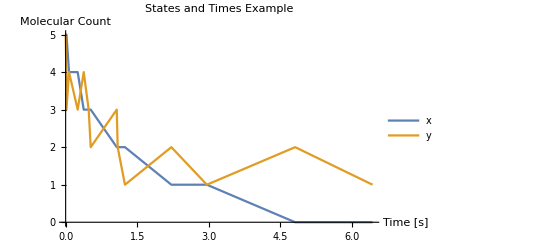

```mathematica
SimulateDirectSSA[rxnsys0,outputTS->False]
PlotLastSimulation[PlotLabel->"States and Times Example"]
```

{{5,5},{4,6},{4,5},{3,6},{3,5},{3,4},{2,5},{2,4},{1,5},{1,4},{1,3},{0,4},{0,3},{0,2},{0,1}}

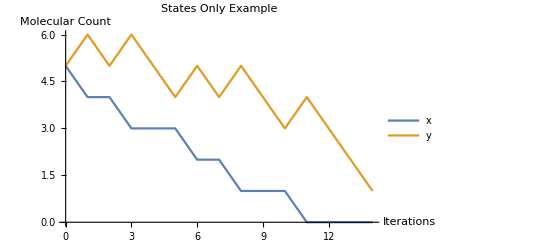

```mathematica
SimulateDirectSSA[rxnsys0,statesOnly->True,outputTS->False]
PlotLastSimulation[PlotLabel->"States Only Example"]
```

{{{5,5},{5,2},{4,3},{2,4},{1,4},{1,2},{1,1},{0,2},{0,1}},{0.,0.143156,0.152393,0.393846,0.590707,0.754231,1.03363,1.72332,1.98501}}

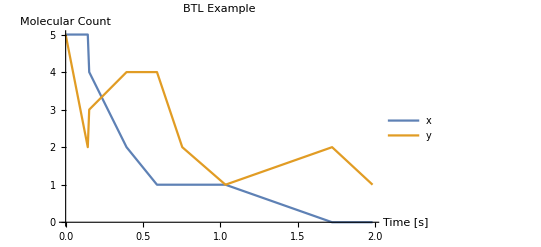

```mathematica
SimulateBoundedTauLeaping[rxnsys0,outputTS->False, epsilon->0.5]
PlotLastSimulation[PlotLabel->"BTL Example"]
```

## Reaction System 1: Demonstrating functionality

```mathematica
rxnsys1={
rxn[0,2x+3y+8z[j-k][j+k],3],
revrxn[z[j+k][j-k],1,4,5],
rxnl[{},{z[j+k][j-k],z[j-k][j+k],x,x},10],
conc[a, 10],
conc[{a,b,x,y},1000],
conc[{z[j+k][j-k],z[j-k][j+k]},2000]
}
SpeciesInRxnsys[rxnsys1]
```

{0 →^3 2 x+3 y+8 z[j-k][j+k] ,z[j+k][j-k] ⇄_5^4 1 ,rxnl[{},{z[j+k][j-k],z[j-k][j+k],x,x},10],conc[a,10],conc[{a,b,x,y},1000],conc[{z[j+k][j-k],z[j-k][j+k]},2000]}

{a,b,x,y,z[j-k][j+k],z[j+k][j-k]}

```mathematica
SpeciesInRxnsys[rxnsys1, z[_][_]]
```

{z[j-k][j+k],z[j+k][j-k]}

```mathematica
SimulateDirectSSA[rxnsys1,iterEnd->15,useIter->True,statesOnly->True,outputTS->False]
```

{{1010,1000,1000,1000,2000,2000},{1010,1000,1000,1000,2000,1999},{1010,1000,1000,1000,2000,1998},{1010,1000,1000,1000,2000,1997},{1010,1000,1000,1000,2000,1996},{1010,1000,1000,1000,2000,1995},{1010,1000,1000,1000,2000,1994},{1010,1000,1000,1000,2000,1993},{1010,1000,1000,1000,2000,1992},{1010,1000,1000,1000,2000,1991},{1010,1000,1000,1000,2000,1990},{1010,1000,1000,1000,2000,1989},{1010,1000,1000,1000,2000,1988},{1010,1000,1000,1000,2000,1987},{1010,1000,1000,1000,2000,1986},{1010,1000,1000,1000,2000,1985}}

```mathematica
SimulateBoundedTauLeaping[rxnsys1,iterEnd->15,useIter->True,outputTS->False]
```

{{{1010,1000,1000,1000,2000,2000},{1010,1000,1000,1000,2000,1965},{1010,1000,1000,1000,2000,1930},{1010,1000,1000,1000,2000,1896},{1010,1000,1000,1000,2000,1862},{1010,1000,1000,1000,2000,1829},{1010,1000,1000,1000,2000,1797},{1010,1000,1000,1000,2000,1765},{1010,1000,1000,1000,2000,1734},{1010,1000,1000,1000,2000,1703},{1010,1000,1000,1000,2000,1673},{1010,1000,1000,1000,2000,1643},{1010,1000,1000,1000,2000,1614},{1010,1000,1000,1000,2000,1585},{1010,1000,1000,1000,2000,1557},{1010,1000,1000,1000,2000,1529}},{0.,0.00602015,0.0101189,0.0152139,0.0189718,0.0238312,0.0270836,0.0307648,0.0357202,0.0398492,0.0450028,0.0504587,0.0539208,0.0581125,0.0619738,0.0670851}}

## Reaction System 2: A deterministic CRN

```mathematica
rxnsys2={
rxn[x1,y+z1,2],
rxn[x2,y+z2,2],
rxn[z1+z2,k,1],
rxn[k+y,0,3],
conc[x1,5000],
conc[x2,15000]
}
SpeciesInRxnsys[rxnsys2]
```

{x1 →^2 y+z1 ,x2 →^2 y+z2 ,z1+z2 →^1 k ,k+y →^3 0 ,conc[x1,5000],conc[x2,15000]}

{k,x1,x2,y,z1,z2}

TemporalData[TimeSeries, <<1>>]

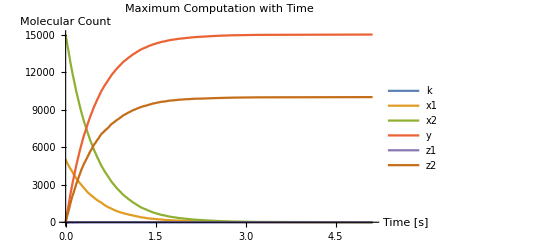

```mathematica
SimulateDirectSSA[rxnsys2]
PlotLastSimulation[PlotLabel->"Maximum Computation with Time"]
```

TemporalData[TimeSeries, <<1>>]

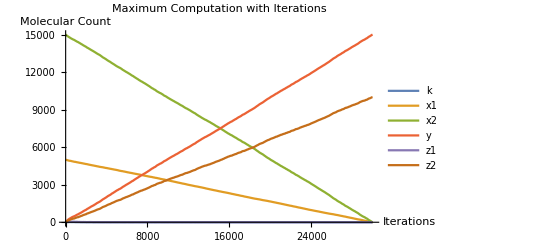

```mathematica
SimulateDirectSSA[rxnsys2,statesOnly->True]
PlotLastSimulation[PlotLabel->"Maximum Computation with Iterations"]
```

TimeSeries[…]

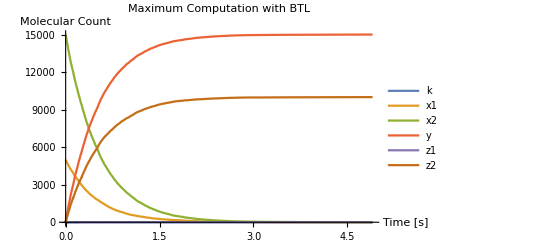

```mathematica
SimulateBoundedTauLeaping[rxnsys2]
PlotLastSimulation[PlotLabel->"Maximum Computation with BTL"]
```

```mathematica
SimulateDirectSSA[rxnsys2,statesOnly->True,finalOnly->True,outputTS->False]
SimulateBoundedTauLeaping[rxnsys2,finalOnly->True,outputTS->False][[1]]
SpeciesInRxnsys[rxnsys2]
```

{{0,0,0,15000,0,10000}}

{{0,0,0,15000,0,10000}}

{k,x1,x2,y,z1,z2}

## Reaction System 3: Demonstrating erroneous input handling

```mathematica
rxnsys3={
rxn[a,b,1],
rxn[c,d,2,3],
rxxn[e,f,4],
reaction[g,h,5],
revrxn[i,j,6,7],
revrxn[k,l,8],
rxnl[{m},{},9],
rxnl[o,p,10],
conc[10],
conc[{a,b,c,d, e, f, g, h},20],
concs[{i, j, k, l, m, o , p},30]
}
SpeciesInRxnsys[rxnsys3]
```

{a →^1 b ,rxn[c,d,2,3],rxxn[e,f,4],reaction[g,h,5],i ⇄_7^6 j ,revrxn[k,l,8],rxnl[{m},{},9],rxnl[o,p,10],conc[10],conc[{a,b,c,d,e,f,g,h},20],concs[{i,j,k,l,m,o,p},30]}

RxnsysToOdesys::rxnargs: rxn[c,d,2,3] is invalid as 3 arguments are expected

RxnsysToOdesys::revrxnargs: revrxn[k,l,8] is invalid as 4 arguments are expected

RxnsysToOdesys::concargs: conc[10] is invalid as 2 arguments are expected

RxnsysToOdesys::rxnllists: rxnl[o,p,10] is invalid as lists are expected for the first and second arguments

$Aborted

```mathematica
SimulateDirectSSA[rxnsys3,finalOnly->True]
PlotLastSimulation[]
```

$Aborted

PlotLastSimulation::finalonlyerr: Error: Cannot plot when finalOnly = True

```mathematica
SimulateBoundedTauLeaping[rxnsys2,iterEnd->0.5,useIter->True,epsilon->1.5];
```

SimulateBoundedTauLeaping::iterenderr: Error: iterEnd (0.5) must be an integer greater than zero

SimulateBoundedTauLeaping::epsilonerr: Error: epsilon (1.5) must be a real number between 0 and 1